# Spatially Adaptive Finite Volume Method For Moment Models

This Mathematica file implements a spatially adaptive finite volume method for moment models. The spatial adaptivity allows the simulation to use a different number of moments (and so different models) in different parts of the domain. Currently, the setting is the following: the domain is divided in 2 subdomains. In the left subdomain, the number of moments (=: ML) is smaller than the number of moments (=: MR) in the right subdomain. 
In this code, the interface between the two models is at the shock.

## Construction of Spatially Adaptive Moment Model

### Source Term

```mathematica
ConstructSourceTerm[nxL_,nxR_,x1_,x2_,momentsLeft_,momentsRight_,Relaxation_,dt_]:=Block[{SourceMatrixLeft,SourceMatrixRight,SourceMatrix,SourceTermVectorLeft,SourceTermVectorRight,SourceTermVector},
(* For the RHS source term, we assume a BGK-type operator and we assume that the source term matrix is a diagonal matrix *)
SourceMatrixLeft =SparseArray[{{i_,i_}/;i>=4:>1},{momentsLeft,momentsLeft}];
SourceMatrixRight =SparseArray[{{i_,i_}/;i>=4:>1},{momentsRight,momentsRight}];

SourceMatrix =ConstantArray[0,{n+2,n+2}];

For[i=1,i<=nxL,i++,
For[j=1,j<i,j++,
SourceMatrix[[i,j]]=ConstantArray[0,{momentsLeft,momentsLeft}]
];
SourceMatrix[[i,i]]=SourceMatrixLeft;
For[j=i+1,j<=nxL,j++,
SourceMatrix[[i,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
];
For[j=nxL+1,j<=n+2,j++,
SourceMatrix[[i,j]]=ConstantArray[0,{momentsLeft,momentsRight}];
];
];

For[i=nxL+1,i<=n+2,i++,
For[j=1,j<=nxL,j++,
SourceMatrix[[i,j]]=ConstantArray[0,{momentsRight,momentsLeft}]
];
For[j=nxL+1,j<i,j++,
SourceMatrix[[i,j]]=ConstantArray[0,{momentsRight,momentsRight}];
];
SourceMatrix[[i,i]]=SourceMatrixRight;
For[j=i+1,j++,j<=n+2,
SourceMatrix[[i,j]]=ConstantArray[0,{momentsRight,momentsRight}];
];
];

SourceTermVectorLeft={0,0,0};
SourceTermVectorRight={0,0,0};

For[i=4,i<=momentsLeft,i++,
SourceTermVectorLeft=Append[SourceTermVectorLeft,1];
SourceTermVectorRight=Append[SourceTermVectorRight,1];
];
For[i=momentsLeft+1,i<=momentsRight,i++,
SourceTermVectorRight=Append[SourceTermVectorRight,1];
];
SourceTermVector={};
For[i=0,i<nxL,i++,
SourceTermVector=Join[SourceTermVector,SourceTermVectorLeft];
];
For[i=nxL,i<=n+1,i++,
SourceTermVector=Join[SourceTermVector,SourceTermVectorRight];
];
(* Obtain source term vector *)
SourceTermVector=-1/Relaxation*SourceTermVector;

(* Obtain Exponential of source term vector *)
SourceTermVector=Exp[SourceTermVector*dt];

SourceTermMatrix=DiagonalMatrix[SourceTermVector];
];
```

### Construction of model at the interface between the two subdomains

#### Using the bigger model

```mathematica
BiggerModelAtInterface[]:=(
RoeBiggerModel[[nxL+2,nxL+1]]=ARight;
RoeBiggerModel[[nxL+2,nxL+1]][[All,-numberOfMomentsDifference;;-1]]=0;
RoeBiggerModel[[nxL+2,nxL+2]]=ConstantArray[0,{momentsRight,momentsRight}];
RoeBiggerModel[[nxL+2,nxL+3]]=-ARight;
ViscosityBiggerModel[[nxL+2,nxL+1]]=ConstantArray[0,{momentsRight,momentsRight}];
ViscosityBiggerModel[[nxL+2,nxL+1]][[All,-numberOfMomentsDifference;;-1]]=0;
ViscosityBiggerModel[[nxL+2,nxL+2]]=ConstantArray[0,{momentsRight,momentsRight}];
ViscosityBiggerModel[[nxL+2,nxL+3]]=ConstantArray[0,{momentsRight,momentsRight}];
)
```

#### Using the extended model

```mathematica
ExtendedModelAtInterface[]:=(
(*BigAMatrix[[nxL+2,nxL+1]]= -1/(2*dx)*(ArrayPad[ALeft,{{0,numberOfMomentsDifference},{0,numberOfMomentsDifference}}]-ArrayPad[QLeft,{{0,numberOfMomentsDifference},{0,numberOfMomentsDifference}}]);
BigAMatrix[[nxL+2,nxL+2]]= -1/(2*dx)*(2*ArrayPad[QLeft,{{0,numberOfMomentsDifference},{0,numberOfMomentsDifference}}]);
BigAMatrix[[nxL+2,nxL+3]]= -1/(2*dx)*(-ArrayPad[ALeft,{{0,numberOfMomentsDifference},{0,numberOfMomentsDifference}}]-ArrayPad[QLeft,{{0,numberOfMomentsDifference},{0,numberOfMomentsDifference}}]);
BigAMatrixFlatten=ArrayFlatten[BigAMatrix];*)
RoeExtendedModel[[nxL+2,nxL+1]]=ATilde;
RoeExtendedModel[[nxL+2,nxL+1]][[All,-numberOfMomentsDifference;;-1]]=0;
(*RoeExtendedModel[[nxL+2,nxL+2]]=ATilde-ARight;*)
RoeExtendedModel[[nxL+2,nxL+2]]=ConstantArray[0,{momentsRight,momentsRight}];
RoeExtendedModel[[nxL+2,nxL+3]]=-ATilde;
ViscosityExtendedModel[[nxL+2,nxL+1]]=-QTilde;
ViscosityExtendedModel[[nxL+2,nxL+1]][[All,-numberOfMomentsDifference;;-1]]=0;
(*ViscosityExtendedModel[[nxL+2,nxL+2]]=QTilde+QRight;*)
ViscosityExtendedModel[[nxL+2,nxL+2]]=2*QTilde;
ViscosityExtendedModel[[nxL+2,nxL+3]]=-QTilde;
)
```

### Construction matrix

```mathematica
ConstructMatrix[nxL_,nxR_,x1_,x2_,dx_,momentsLeft_,momentsRight_,Relaxation_,dt_]:=Block[{},

(* Define the model matrices *)
ALeft=SparseArray[{{i_,j_}/;i-j==1:>Sqrt[j],{i_,j_}/;j-i==1:>Sqrt[i]},{momentsLeft,momentsLeft}];
ARight=SparseArray[{{i_,j_}/;i-j==1:>Sqrt[j],{i_,j_}/;j-i==1:>Sqrt[i]},{momentsRight,momentsRight}];
ATilde=ARight;
ATilde[[-numberOfMomentsDifference;;-1,All]]=0;

(* Define the numerical viscosity matrices *)
QLeft=IdentityMatrix[momentsLeft];
QRight=IdentityMatrix[momentsRight];
QTilde=QRight;
QTilde[[-numberOfMomentsDifference;;-1,All]]=0;

RoeWeightedSum = ConstantArray[0,{n+2,n+2}];
ViscosityWeightedSum=ConstantArray[0,{n+2,n+2}];

RoeBiggerModel = ConstantArray[0,{n+2,n+2}];
ViscosityBiggerModel=ConstantArray[0,{n+2,n+2}];

RoeExtendedModel = ConstantArray[0,{n+2,n+2}];
ViscosityExtendedModel=ConstantArray[0,{n+2,n+2}];

(* CREATE THE SPATIAL DISCRETIZATION MATRIX BLOCK BY BLOCK *)

(* First row is a ghost row *)
For[j=1,j<=nxL,j++,
RoeWeightedSum[[1,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
ViscosityWeightedSum[[1,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
];

For[j=nxL+1,j<=n+2,j++,
RoeWeightedSum[[1,j]]=ConstantArray[0,{momentsLeft,momentsRight}];
ViscosityWeightedSum[[1,j]]=ConstantArray[0,{momentsLeft,momentsRight}];
];


(* Rows corresponding to moment model of order ML *)
For[i=2,i<nxL,i++,
RoeWeightedSum[[i,i-1]]=ALeft;
RoeWeightedSum[[i,i]]=ConstantArray[0,{momentsLeft,momentsLeft}];
RoeWeightedSum[[i,i+1]]=-ALeft;
ViscosityWeightedSum[[i,i-1]]=-QLeft;
ViscosityWeightedSum[[i,i]]=2*QLeft;
ViscosityWeightedSum[[i,i+1]]=-QLeft;

For[j=1,j<i-1,j++,
RoeWeightedSum[[i,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
ViscosityWeightedSum[[i,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
];

For[j=i+2,j<=nxL,j++,
RoeWeightedSum[[i,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
ViscosityWeightedSum[[i,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
];

For[j=nxL+1,j<=n+2,j++,
RoeWeightedSum[[i,j]]=ConstantArray[0,{momentsLeft,momentsRight}];
ViscosityWeightedSum[[i,j]]=ConstantArray[0,{momentsLeft,momentsRight}];
];
];

(* Row nxL (corresponds to vector nxL-1 because of the introduced ghost rows *) 
RoeWeightedSum[[nxL,nxL-1]]=ALeft;
RoeWeightedSum[[nxL,nxL]]=ConstantArray[0,{momentsLeft,momentsLeft}];
RoeWeightedSum[[nxL,nxL+1]]=-ArrayPad[ALeft,{{0,0},{0,numberOfMomentsDifference}}];
ViscosityWeightedSum[[nxL,nxL-1]]=-QLeft;
ViscosityWeightedSum[[nxL,nxL]]=2*QLeft;
ViscosityWeightedSum[[nxL,nxL+1]]=-ArrayPad[QLeft,{{0,0},{0,numberOfMomentsDifference}}];

For[j=1,j<nxL-1,j++,
RoeWeightedSum[[nxL,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
ViscosityWeightedSum[[nxL,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
];

For[j=nxL+2,j<=n+2,j++,
RoeWeightedSum[[nxL,j]]=ConstantArray[0,{momentsLeft,momentsRight}];
ViscosityWeightedSum[[nxL,j]]=ConstantArray[0,{momentsLeft,momentsRight}];
];


(* Row nxL+1 (correspond to vector nxL because of the introduced  ghost rows *)
RoeWeightedSum[[nxL+1,nxL]]=ArrayPad[ALeft,{{0,numberOfMomentsDifference},{0,0}}];
RoeWeightedSum[[nxL+1,nxL+1]]=ConstantArray[0,{momentsRight,momentsRight}];
RoeWeightedSum[[nxL+1,nxL+2]]=-ATilde;
ViscosityWeightedSum[[nxL+1,nxL]]=-ArrayPad[QLeft,{{0,numberOfMomentsDifference},{0,0}}];
ViscosityWeightedSum[[nxL+1,nxL+1]]=2*ArrayPad[QLeft,{{0,numberOfMomentsDifference},{0,numberOfMomentsDifference}}];
ViscosityWeightedSum[[nxL+1,nxL+2]]=-QTilde;

For[j=1,j<nxL,j++,
RoeWeightedSum[[nxL+1,j]]=ConstantArray[0,{momentsRight,momentsLeft}];
ViscosityWeightedSum[[nxL+1,j]]=ConstantArray[0,{momentsRight,momentsLeft}];
];

For[j=nxL+3,j<=n+2,j++,
RoeWeightedSum[[nxL+1,j]]=ConstantArray[0,{momentsRight,momentsRight}];
ViscosityWeightedSum[[nxL+1,j]]=ConstantArray[0,{momentsRight,momentsRight}];
];

(* Row nxL+2 (corresponds to vector nxL+1 because of the introduced ghost rows *)
(* Remark: default is using the bigger matrix *)

RoeWeightedSum[[nxL+2,nxL+1]]=ARight;
RoeWeightedSum[[nxL+2,nxL+1]][[All,-numberOfMomentsDifference;;-1]]=0;
RoeWeightedSum[[nxL+2,nxL+2]]=ConstantArray[0,{momentsRight,momentsRight}];
RoeWeightedSum[[nxL+2,nxL+3]]=-ARight;
ViscosityWeightedSum[[nxL+2,nxL+1]]=-QRight;
ViscosityWeightedSum[[nxL+2,nxL+1]][[All,-numberOfMomentsDifference;;-1]]=0;
ViscosityWeightedSum[[nxL+2,nxL+2]]=2*QRight;
ViscosityWeightedSum[[nxL+2,nxL+3]]=-QRight;

For[j=1,j<=nxL,j++,
RoeWeightedSum[[nxL+2,j]]=ConstantArray[0,{momentsRight,momentsLeft}];
ViscosityWeightedSum[[nxL+2,j]]=ConstantArray[0,{momentsRight,momentsLeft}];
];

For[j=nxL+4,j<=n+2,j++,
RoeWeightedSum[[nxL+2,j]]=ConstantArray[0,{momentsRight,momentsRight}];
ViscosityWeightedSum[[nxL+2,j]]=ConstantArray[0,{momentsRight,momentsRight}];
];


(* Rows corresponding to moment model of order MR (without the last one) *)
For[i=nxL+3,i<n+2,i++,
RoeWeightedSum[[i,i-1]]=ARight;
RoeWeightedSum[[i,i]]=ConstantArray[0,{momentsRight,momentsRight}];
RoeWeightedSum[[i,i+1]]=-ARight;

ViscosityWeightedSum[[i,i-1]]=-QRight;
ViscosityWeightedSum[[i,i]]=2*QRight;
ViscosityWeightedSum[[i,i+1]]=-QRight;

For[j=1,j<=nxL,j++,
RoeWeightedSum[[i,j]]=ConstantArray[0,{momentsRight,momentsLeft}];
ViscosityWeightedSum[[i,j]]=ConstantArray[0,{momentsRight,momentsLeft}];
];

For[j=nxL+1,j<i-1,j++,
RoeWeightedSum[[i,j]]=ConstantArray[0,{momentsRight,momentsRight}];
ViscosityWeightedSum[[i,j]]=ConstantArray[0,{momentsRight,momentsRight}];
];

For[j=i+2,j<=n+2,j++,
RoeWeightedSum[[i,j]]=ConstantArray[0,{momentsRight,momentsRight}];
ViscosityWeightedSum[[i,j]]=ConstantArray[0,{momentsRight,momentsRight}];
];
];


(* Last rows are ghost rows *)
For[j=1,j<=nxL,j++,
RoeWeightedSum[[n+2,j]]=ConstantArray[0,{momentsRight,momentsLeft}];
ViscosityWeightedSum[[n+2,j]]=ConstantArray[0,{momentsRight,momentsLeft}];
];

For[j=nxL+1,j<=n+2,j++,
RoeWeightedSum[[n+2,j]]=ConstantArray[0,{momentsRight,momentsRight}];
ViscosityWeightedSum[[n+2,j]]=ConstantArray[0,{momentsRight,momentsRight}];
];

RoeBiggerModel=RoeWeightedSum;
ViscosityBiggerModel=ViscosityWeightedSum;
BiggerModelAtInterface[];

RoeExtendedModel=RoeWeightedSum;
ViscosityExtendedModel=ViscosityWeightedSum;
ExtendedModelAtInterface[];

RoeWeightedSumFlatten = ArrayFlatten[RoeWeightedSum];
ViscosityWeightedSumFlatten = ArrayFlatten[ViscosityWeightedSum];

RoeBiggerModelFlatten = ArrayFlatten[RoeBiggerModel];
ViscosityBiggerModelFlatten = ArrayFlatten[ViscosityBiggerModel];

RoeExtendedModelFlatten = ArrayFlatten[RoeExtendedModel];
ViscosityExtendedModelFlatten = ArrayFlatten[ViscosityExtendedModel];

(* For the RHS source term, we assume a BGK-type operator and we assume that the source term matrix is a diagonal matrix *)

ConstructSourceTerm[nxL,nxR,x1,x2,momentsLeft,momentsRight,Relaxation,dt];

(* Obtain transport part of spatial discretization matrix from Roe block matrix and viscosity block matrix *)
BigAMatrixWeightedSum=-1.0/(2*dx)*(RoeWeightedSum+ViscosityWeightedSum);
BigAMatrixWeightedSumFlatten = -1.0/(2*dx)*(RoeWeightedSumFlatten+ViscosityWeightedSumFlatten);

BigAMatrixBiggerModel=-1.0/(2*dx)*(RoeBiggerModel+ViscosityBiggerModel);
BigAMatrixBiggerModelFlatten = -1.0/(2*dx)*(RoeBiggerModelFlatten+ViscosityBiggerModelFlatten);

BigAMatrixExtendedModel=-1.0/(2*dx)*(RoeExtendedModel+ViscosityExtendedModel);
BigAMatrixExtendedModelFlatten = -1.0/(2*dx)*(RoeExtendedModelFlatten+ViscosityExtendedModelFlatten);

];
```

## Construction of Reference Solution

### Source Term

```mathematica
ConstructSourceTermReference[nxL_,nxR_,x1_,x2_,momentsLeft_,momentsRight_,Relaxation_,dt_]:=Block[{SourceMatrixRight,SourceMatrixReference,SourceTermVectorReference,SourceTermVectorRight},
SourceMatrixReference =ConstantArray[0,{n+2,n+2}];

SourceMatrixRight =SparseArray[{{i_,i_}/;i>=4:>1},{momentsRight,momentsRight}];

For[i=1,i<=n+2,i++,
For[j=1,j<i,j++,
SourceMatrixReference[[i,j]]=ConstantArray[0,{momentsRight,momentsRight}]
];
SourceMatrixReference[[i,i]]=SourceMatrixRight;
For[j=i+1,j<=n+2,j++,
SourceMatrixReference[[i,j]]=ConstantArray[0,{momentsRight,momentsRight}];
];
];

SourceTermVectorRight={0,0,0};

For[i=4,i<=momentsRight,i++,
SourceTermVectorRight=Append[SourceTermVectorRight,1];
];

SourceTermVectorReference={};
For[i=0,i<=n+1,i++,
SourceTermVectorReference=Join[SourceTermVectorReference,SourceTermVectorRight];
];

(* Obtain source term vector *)
SourceTermVectorReference=-1/Relaxation*SourceTermVectorReference;

(* Obtain Exponential of source term vector *)
SourceTermVectorReference=Exp[SourceTermVectorReference*dt];

SourceTermMatrixReference=DiagonalMatrix[SourceTermVectorReference];
];
```

### Construction matrix

```mathematica
ConstructMatrixReference[nxL_,nxR_,x1_,x2_,dx_,momentsLeft_,momentsRight_,Relaxation_,dt_]:=Block[{RoeReference,ViscosityReference},
(* AS REFERENCE SOLUTION, WE CONSIDER THE SOLUTION WE OBTAIN BY TAKING THE BIGGER MATRIX EVERYWHERE *)

RoeReference = ConstantArray[0,{n+2,n+2}];
ViscosityReference=ConstantArray[0,{n+2,n+2}];

(* CREATE THE SPATIAL DISCRETIZATION MATRIX BLOCK BY BLOCK *)

(* First row is a ghost row *)
For[j=1,j<=n+2,j++,
RoeReference[[1,j]]=ConstantArray[0,{momentsRight,momentsRight}];
ViscosityReference[[1,j]]=ConstantArray[0,{momentsRight,momentsRight}];
]


(* All rows apart from the first and the last *)
For[i=2,i<=n+1,i++,
RoeReference[[i,i-1]]=ARight;
RoeReference[[i,i]]=ConstantArray[0,{momentsRight,momentsRight}];
RoeReference[[i,i+1]]=-ARight;
ViscosityReference[[i,i-1]]=-QRight;
ViscosityReference[[i,i]]=2*QRight;
ViscosityReference[[i,i+1]]=-QRight;

For[j=1,j<i-1,j++,
RoeReference[[i,j]]=ConstantArray[0,{momentsRight,momentsRight}];
ViscosityReference[[i,j]]=ConstantArray[0,{momentsRight,momentsRight}];
];

For[j=i+2,j<=n+2,j++,
RoeReference[[i,j]]=ConstantArray[0,{momentsRight,momentsRight}];
ViscosityReference[[i,j]]=ConstantArray[0,{momentsRight,momentsRight}];
];
];

(* Last rows are ghost rows *)
For[j=1,j<=n+2,j++,
RoeReference[[n+2,j]]=ConstantArray[0,{momentsRight,momentsRight}];
ViscosityReference[[n+2,j]]=ConstantArray[0,{momentsRight,momentsRight}];
];

ConstructSourceTermReference[nxL,nxR,x1,x2,momentsLeft,momentsRight,Relaxation,dt];

RoeFlattenReference = ArrayFlatten[RoeReference];
ViscosityFlattenReference = ArrayFlatten[ViscosityReference];

(* Obtain transport part of spatial discretization matrix from Roe block matrix and viscosity block matrix *)
BigAMatrixReference=-1.0/(2*dx)*(RoeReference+ViscosityReference);
BigAMatrixFlattenReference = -1.0/(2*dx)*(RoeFlattenReference+ViscosityFlattenReference);
];
```

## Simulation Setup

### Construct vector with initial values

```mathematica
InitializeVector[initialValuesLeft_,initialValuesRight_,epsilon_,momentsBig_,momentsLeft_,momentsRight_]:=
Block[{momentSmall,initialValuesLeft2,initialValuesRight2,initialValuesLeftReference,initialValuesRightReference,values,valuesReference},

momentSmall=epsilon;

initialValuesLeft2=initialValuesLeft;
initialValuesRight2=initialValuesRight;
initialValuesLeftReference =initialValuesLeft;
initialValuesRightReference=initialValuesRight;

For[i=4,i<=momentsLeft,i++,
initialValuesLeft2=Append[initialValuesLeft2,momentsBig];
initialValuesRight2=Append[initialValuesRight2,momentsBig];
initialValuesLeftReference=Append[initialValuesLeftReference,momentsBig];
initialValuesRightReference=Append[initialValuesRightReference,momentsBig];
];
For[i=momentsLeft+1,i<=momentsRight,i++,
initialValuesRight2=Append[initialValuesRight2,momentSmall];
initialValuesLeftReference=Append[initialValuesLeftReference,momentSmall];
initialValuesRightReference=Append[initialValuesRightReference,momentSmall];
];

(* Construct initial vector *)
Wraw={};
WrawReference={};
For[i=0,i<nxL,i++,
values[i]=initialValuesLeft2;
Wraw=Join[Wraw,values[i]];
valuesReference[i]=initialValuesLeftReference;
WrawReference=Join[WrawReference,valuesReference[i]];
];
values[nxL]=ArrayPad[initialValuesLeft2,{0,numberOfMomentsDifference}]; (* Take initial values from the left and add zeroes *)
Wraw=Join[Wraw,values[nxL]];
valuesReference[nxL]=initialValuesLeftReference;
WrawReference=Join[WrawReference,valuesReference[nxL]];
For[i=1,i<=nxR+1,i++,
values[i+nxL]=initialValuesRight2;
Wraw=Join[Wraw,values[i+nxL]];
valuesReference[i]=initialValuesRightReference;
WrawReference=Join[WrawReference,valuesReference[i]];
];
];
```

### Set up model

```mathematica
InitializeModel[nxL_,nxR_,x1_,x2_,momentsLeft_,momentsRight_,initialValuesLeft_,initialValuesRight_,epsilon_,momentsBig_,Relaxation_]:=Block[{dx,values,valuesReference},

numberOfMomentsDifference=momentsRight-momentsLeft;
n=nxL+nxR;
dx=(x2-x1)/n;

InitializeVector[initialValuesLeft,initialValuesRight,epsilon,momentsBig,momentsLeft,momentsRight];

(* Initialize the collection of the moments *)
moments=Table[moment[i],{i,0,momentsRight-1}];
momentsReference=Table[momentReference[i],{i,0,momentsRight-1}];
momentsLoop=Table[moment[i],{i,0,momentsRight-1}];
momentsReferenceLoop=Table[momentReferenceLoop[i],{i,0,momentsRight-1}];
For[i=0,i<momentsRight,i++,
moment[i]={};
momentReference[i]={};
];
(* Choose time step *)
dt=0.1dx;

ConstructMatrix[nxL,nxR,x1,x2,dx,momentsLeft,momentsRight,Relaxation,dt];
ConstructMatrixReference[nxL,nxR,x1,x2,dx,momentsLeft,momentsRight,Relaxation,dt];
];
```

## Simulation Functions

### Spatially Adaptive Moment Model With Weighted Sum

```mathematica
FiniteVolumeSchemeWeightedSum[tend_]:=Block[{norm,normRemainder,WeightedSumRoe,WeightedSumViscosity,modelDiffA,modelDiffQ},
W=Wraw;
time= 0.0;
step=0;

{timeSpatiallyAdaptive,outputSpatiallyAdaptive}=
AbsoluteTiming[
While[time<tend,
(* Compute the values of the point s0 along the path *)

norm=0;
For[i=1,i<=momentsLeft,i++,
norm+=(W[[momentsLeft*nxL+i]]-W[[momentsLeft*nxL+momentsRight+i]])^2;
];
normRemainder=0;
For[i=momentsLeft+1,i<=momentsRight,i++,
normRemainder+=W[[momentsLeft*nxL+momentsRight+i]]^2;
];
If[Sqrt[norm]+Sqrt[normRemainder]==0,s0=0,s0=Sqrt[norm]/(Sqrt[norm]+Sqrt[normRemainder])];

(* s0=1.0; *)

(* THE SYSTEM MATRIX HERE IS A WEIGHTED SUM OF THE BIGGER MATRIX AND THE SMALLER MATRIX *)


WeightedSumRoe=s0*ATilde+(1-s0)*ARight;
WeightedSumRoe[[All,-numberOfMomentsDifference;;-1]]=0;
WeightedSumViscosity=s0*QTilde+(1-s0)*QRight;
WeightedSumViscosity[[All,-numberOfMomentsDifference;;-1]]=0;
modelDiffA=ATilde-ARight;
modelDiffQ=QTilde-QRight;
modelDiffA[[All,-numberOfMomentsDifference;;-1]]=0;
modelDiffQ[[All,-numberOfMomentsDifference;;-1]]=0;
(*BigAMatrix[[nxL+2,nxL+1]]= -1/(2*dx)*(WeightedSumRoe-WeightedSumViscosity);
BigAMatrix[[nxL+2,nxL+2]]= -1/(2*dx)*(s0*modelDiffA+2*QRight+s0*(modelDiffQ));
BigAMatrix[[nxL+2,nxL+3]]= -1/(2*dx)*(-ARight-QRight);*)
BigAMatrixWeightedSum[[nxL+2,nxL+1]]= -1/(2*dx)*(WeightedSumRoe-WeightedSumViscosity);
BigAMatrixWeightedSum[[nxL+2,nxL+2]]= -1/(2*dx)*(2*QRight);
BigAMatrixWeightedSum[[nxL+2,nxL+3]]= -1/(2*dx)*(-ARight-QRight);

(* USING THE SMALLER MATRIX *)
(*
BigAMatrix[[nxL+2,nxL+1]]= -1/(2*dx)*(ArrayPad[ALeft,{{0,numberOfMomentsDifference},{0,numberOfMomentsDifference}}]-ArrayPad[QLeft,{{0,numberOfMomentsDifference},{0,numberOfMomentsDifference}}]);
BigAMatrix[[nxL+2,nxL+2]]= -1/(2*dx)*(2*ArrayPad[QLeft,{{0,numberOfMomentsDifference},{0,numberOfMomentsDifference}}]);
BigAMatrix[[nxL+2,nxL+3]]= -1/(2*dx)*(-ArrayPad[ALeft,{{0,numberOfMomentsDifference},{0,numberOfMomentsDifference}}]-ArrayPad[QLeft,{{0,numberOfMomentsDifference},{0,numberOfMomentsDifference}}]);
*)

BigAMatrixWeightedSumFlatten=ArrayFlatten[BigAMatrixWeightedSum];

(* Transport step *)
W=W+dt*BigAMatrixWeightedSumFlatten.W;

(* Relaxation step *)
W=SourceTermMatrix.W;

(* Update boundary conditions *)
For[i=0,i<momentsLeft,i++,
W[[i+1]]=W[[i+1+momentsLeft]];
];
For[i=0,i<momentsRight,i++,
W[[momentsLeft*nxL+momentsRight*(nxR+1)+i+1]]=W[[momentsLeft*nxL+momentsRight*nxR+i+1]];
];

(* Update collection of each moment *)
For[i=0,i<momentsRight,i++,
momentLoop[i]={};
];

For[i=0,i<nxL,i++,
For[j=0,j<momentsLeft,j++,
momentLoop[j]=Append[momentLoop[j],W[[momentsLeft*i+j+1]]]
]
];
For[i=0,i<=nxR+1,i++,
For[j=0,j<momentsRight,j++,
momentLoop[j]=Append[momentLoop[j],W[[momentsLeft*nxL+momentsRight*i+j+1]]]
]
];

For[i=0,i<momentsRight,i++,
moment[i]=momentLoop[i];
];

(* For the Hermite spectral method: f0=ρ, f1=ρu, f2=1/(√2)(ρT+ρu^2-ρ) *)
density=moment[0];
velocity=moment[1]/density;
temperature=(√2*moment[2]-density*velocity*velocity+density)/density;


time = time+dt;
step++;
]
];
];
```

### Spatially Adaptive Moment Model with using the bigger model at the interface between the two models

```mathematica
FiniteVolumeSchemeBiggerModel[tend_]:=(

W=Wraw;
time= 0.0;
step=0;

{timeSpatiallyAdaptive,outputSpatiallyAdaptive}=
AbsoluteTiming[
While[time<tend,

(* Transport step *)
W=W+dt*BigAMatrixBiggerModelFlatten.W;

(* Relaxation step *)
W=SourceTermMatrix.W;

(* Update boundary conditions *)
For[i=0,i<momentsLeft,i++,
W[[i+1]]=W[[i+1+momentsLeft]];
];
For[i=0,i<momentsRight,i++,
W[[momentsLeft*nxL+momentsRight*(nxR+1)+i+1]]=W[[momentsLeft*nxL+momentsRight*nxR+i+1]];
];

(* Update collection of each moment *)
For[i=0,i<momentsRight,i++,
momentLoop[i]={};
];

For[i=0,i<nxL,i++,
For[j=0,j<momentsLeft,j++,
momentLoop[j]=Append[momentLoop[j],W[[momentsLeft*i+j+1]]]
]
];
For[i=0,i<=nxR+1,i++,
For[j=0,j<momentsRight,j++,
momentLoop[j]=Append[momentLoop[j],W[[momentsLeft*nxL+momentsRight*i+j+1]]]
]
];

For[i=0,i<momentsRight,i++,
moment[i]=momentLoop[i];
];

(* For the Hermite spectral method: f0=ρ, f1=ρu, f2=1/(√2)(ρT+ρu^2-ρ) *)
density=moment[0];
velocity=moment[1]/density;
temperature=(√2*moment[2]-density*velocity*velocity+density)/density;


time = time+dt;
step++;
]
];
);
```

### Spatially Adaptive Moment Model with using the model for the extended vector at the interface between the two models

```mathematica
FiniteVolumeSchemeExtendedModel[tend_]:=(

W=Wraw;
time= 0.0;
step=0;

{timeSpatiallyAdaptive,outputSpatiallyAdaptive}=
AbsoluteTiming[
While[time<tend,

(* Transport step *)
W=W+dt*BigAMatrixExtendedModelFlatten.W;

(* Relaxation step *)
W=SourceTermMatrix.W;

(* Update boundary conditions *)
For[i=0,i<momentsLeft,i++,
W[[i+1]]=W[[i+1+momentsLeft]];
];
For[i=0,i<momentsRight,i++,
W[[momentsLeft*nxL+momentsRight*(nxR+1)+i+1]]=W[[momentsLeft*nxL+momentsRight*nxR+i+1]];
];

(* Update collection of each moment *)
For[i=0,i<momentsRight,i++,
momentLoop[i]={};
];

For[i=0,i<nxL,i++,
For[j=0,j<momentsLeft,j++,
momentLoop[j]=Append[momentLoop[j],W[[momentsLeft*i+j+1]]]
]
];
For[i=0,i<=nxR+1,i++,
For[j=0,j<momentsRight,j++,
momentLoop[j]=Append[momentLoop[j],W[[momentsLeft*nxL+momentsRight*i+j+1]]]
]
];

For[i=0,i<momentsRight,i++,
moment[i]=momentLoop[i];
];

(* For the Hermite spectral method: f0=ρ, f1=ρu, f2=1/(√2)(ρT+ρu^2-ρ) *)
density=moment[0];
velocity=moment[1]/density;
temperature=(√2*moment[2]-density*velocity*velocity+density)/density;


time = time+dt;
step++;
]
];
);
```

### Reference Solution

```mathematica
FiniteVolumeSchemeReference[tend_]:=Block[{},
WReference=WrawReference;
time= 0.0;
step=0;

{timeReference,outputReference}=
AbsoluteTiming[
While[time<tend,
(* Transport step *)
WReference=WReference+dt*BigAMatrixFlattenReference.WReference;

(* Relaxation step *)
WReference=SourceTermMatrixReference.WReference;

(* Update boundary conditions *)
For[i=0,i<momentsRight,i++,
WReference[[i+1]]=WReference[[i+1+momentsRight]];
WReference[[momentsRight*nxL+momentsRight*(nxR+1)+i+1]]=WReference[[momentsRight*nxL+momentsRight*nxR+i+1]];
];

(* Update collection of each moment *)
For[i=0,i<momentsRight,i++,
momentReferenceLoop[i]={};
];

For[i=0,i<=n+1,i++,
For[j=0,j<momentsRight,j++,
momentReferenceLoop[j]=Append[momentReferenceLoop[j],WReference[[momentsRight*i+j+1]]];
];
];

For[i=0,i<momentsRight,i++,
momentReference[i]= momentReferenceLoop[i];
];

(* For the Hermite spectral method: f0=ρ, f1=ρu, f2=1/(√2)(ρT+ρu^2-ρ) *)
densityReference=momentReference[0];
velocityReference=momentReference[1]/densityReference;
temperatureReference=(√2*momentReference[2]-densityReference*velocityReference*velocityReference+densityReference)/densityReference;

time = time+dt;
step++;
]
];
];
```

### Comparison between reference solution and spatially adaptive moment model

```mathematica
FiniteVolumeSchemeComparison[tend_]:=Block[{norm,normRemainder,WeightedSumRoe,WeightedSumViscosity,modelDiffA,modelDiffQ},
W=Wraw;
WReference=WrawReference;
time= 0.0;
step=0;

{timeSpatiallyAdaptive,outputSpatiallyAdaptive}=
AbsoluteTiming[
While[time<tend,
(* Compute the values of the point s0 along the path *)

norm=0;
For[i=1,i<=momentsLeft,i++,
norm+=(W[[momentsLeft*nxL+i]]-W[[momentsLeft*nxL+momentsRight+i]])^2;
];
normRemainder=0;
For[i=momentsLeft+1,i<=momentsRight,i++,
normRemainder+=W[[momentsLeft*nxL+momentsRight+i]]^2;
];
If[Sqrt[norm]+Sqrt[normRemainder]==0,s0=0,s0=Sqrt[norm]/(Sqrt[norm]+Sqrt[normRemainder])];

(* s0=0; *)

(* THE SYSTEM MATRIX HERE IS A WEIGHTED SUM OF THE BIGGER MATRIX AND THE SMALLER MATRIX *)


WeightedSumRoe=s0*ATilde+(1-s0)*ARight;
WeightedSumRoe[[All,-numberOfMomentsDifference;;-1]]=0;
WeightedSumViscosity=s0*QTilde+(1-s0)*QRight;
WeightedSumViscosity[[All,-numberOfMomentsDifference;;-1]]=0;
modelDiffA=ATilde-ARight;
modelDiffQ=QTilde-QRight;
modelDiffA[[All,-numberOfMomentsDifference;;-1]]=0;
modelDiffQ[[All,-numberOfMomentsDifference;;-1]]=0;
BigAMatrix[[nxL+2,nxL+1]]= -1/(2*dx)*(WeightedSumRoe-WeightedSumViscosity);
BigAMatrix[[nxL+2,nxL+2]]= -1/(2*dx)*(s0*modelDiffA+2*QRight+s0*(modelDiffQ));
BigAMatrix[[nxL+2,nxL+3]]= -1/(2*dx)*(-ARight-QRight);


(* USING THE SMALLER MATRIX *)
(*
BigAMatrix[[nxL+2,nxL+1]]= -1/(2*dx)*(ArrayPad[ALeft,{{0,numberOfMomentsDifference},{0,numberOfMomentsDifference}}]-ArrayPad[QLeft,{{0,numberOfMomentsDifference},{0,numberOfMomentsDifference}}]);
BigAMatrix[[nxL+2,nxL+2]]= -1/(2*dx)*(2*ArrayPad[QLeft,{{0,numberOfMomentsDifference},{0,numberOfMomentsDifference}}]);
BigAMatrix[[nxL+2,nxL+3]]= -1/(2*dx)*(-ArrayPad[ALeft,{{0,numberOfMomentsDifference},{0,numberOfMomentsDifference}}]-ArrayPad[QLeft,{{0,numberOfMomentsDifference},{0,numberOfMomentsDifference}}]);
*)

BigAMatrixFlatten=ArrayFlatten[BigAMatrix];

(* Transport step *)
W=W+dt*BigAMatrixFlatten.W;
WReference=WReference+dt*BigAMatrixFlattenReference.WReference;

(* Relaxation step *)
W=SourceTermMatrix.W;
WReference=SourceTermMatrixReference.WReference;

(* Update boundary conditions *)
For[i=0,i<momentsLeft,i++,
W[[i+1]]=W[[i+1+momentsLeft]];
];
For[i=0,i<momentsRight,i++,
W[[momentsLeft*nxL+momentsRight*(nxR+1)+i+1]]=W[[momentsLeft*nxL+momentsRight*nxR+i+1]];
WReference[[i+1]]=WReference[[i+1+momentsRight]];
WReference[[momentsRight*nxL+momentsRight*(nxR+1)+i+1]]=WReference[[momentsRight*nxL+momentsRight*nxR+i+1]];
];

(* Update collection of each moment *)
For[i=0,i<momentsRight,i++,
momentLoop[i]={};
momentReferenceLoop[i]={};
];

For[i=0,i<nxL,i++,
For[j=0,j<momentsLeft,j++,
momentLoop[j]=Append[momentLoop[j],W[[momentsLeft*i+j+1]]]
]
];
For[i=0,i<=nxR+1,i++,
For[j=0,j<momentsRight,j++,
momentLoop[j]=Append[momentLoop[j],W[[momentsLeft*nxL+momentsRight*i+j+1]]]
]
];

For[i=0,i<=n+1,i++,
For[j=0,j<momentsRight,j++,
momentReferenceLoop[j]=Append[momentReferenceLoop[j],WReference[[momentsRight*i+j+1]]];
];
];

For[i=0,i<momentsRight,i++,
moment[i]=momentLoop[i];
momentReference[i]= momentReferenceLoop[i];
];

(* For the Hermite spectral method: f0=ρ, f1=ρu, f2=1/(√2)(ρT+ρu^2-ρ) *)
density=moment[0];
velocity=moment[1]/density;
temperature=(√2*moment[2]-density*velocity*velocity+density)/density;
densityReference=momentReference[0];
velocityReference=momentReference[1]/densityReference;
temperatureReference=(√2*momentReference[2]-densityReference*velocityReference*velocityReference+densityReference)/densityReference;


time = time+dt;
step++;
]
];
];
```

## Numerical Data Post Processing

```mathematica
(* For the Hermite spectral method: f0=ρ, f1=ρu, f2=1/(√2)(ρT+ρu^2-ρ) *)
density=moment[0];
velocity=moment[1]/density;
temperature=(√2*moment[2]-density*velocity*velocity+density)/density;
densityReference=momentReference[0];
velocityReference=momentReference[1]/densityReference;
temperatureReference=(√2*momentReference[2]-densityReference*velocityReference*velocityReference+densityReference)/densityReference;
```

## Numerical Results

### Template

```mathematica
(* Choose number of cells in left and right subdomain *)
nxL = 100;
nxR = 100;

(* Choose boundaries of the spatial domain *)
x1=-10;
x2=10;

dx=(x2-x1)/(nxL+nxR);

(* Choose number of moments in left and right subdomain *)
momentsLeft=4;
momentsRight=5;

(* Choose initial values *)
initialValuesLeft={1,1,1};
initialValuesRight={1,1,1};
epsilon=1.0;
momentsBig=0.0;

(* Choose relaxation parameter *)
Relaxation=1.0;

(* Choose end time *)
tend=0.02;

InitializeModel[nxL,nxR,x1,x2,momentsLeft,momentsRight,initialValuesLeft,initialValuesRight,epsilon,momentsBig,Relaxation]
```

```mathematica
(*Dynamic[ListPlot[moment[3],PlotRange->{-1,1}]]*)
Dynamic[ListPlot[moment[3]]]
FiniteVolumeSchemeBiggerModel[tend]
```

```mathematica
ARight//MatrixForm
```

(0 | 1 | 0 | 0 | 0
1 | 0 | √2 | 0 | 0
0 | √2 | 0 | √3 | 0
0 | 0 | √3 | 0 | 2
0 | 0 | 0 | 2 | 0)

### Opposite velocity

```mathematica
nxL = 100;
nxR = 100;

x1=-10;
x2=10;

dx=(x2-x1)/(nxL+nxR);

momentsLeft=4;
momentsRight=6;

Relaxation=1.0;

tend=20;

InitializeModel[nxL,nxR,x1,x2,momentsLeft,momentsRight,Relaxation]
```

## Stability analysis

### Eigenvalues of the full spatial discretization matrix

```mathematica
(* Obtain the full spatial discretization matrix *)

StabilityMatrix = BigAMatrixFlatten+SourceTermMatrix;
```

```mathematica
(* This computes the eigenvalues of the spatial discretization matrix *)
eigenvaluesStabilityMatrix=Eigenvalues[StabilityMatrix];
realPartEigenvalues=Re[eigenvaluesStabilityMatrix];
realPartEigenvaluesSorted=Sort[realPartEigenvalues];
```

```mathematica
(* This computes the eigenvalue with the biggest real part *)
Eigenvalues[StabilityMatrix,1,Method->{"Arnoldi","Criteria"->"RealPart","MaxIterations"->10000}]
```

Eigenvalues::maxit2: Warning: maximum number of iterations, 10000, has been reached by the Arnoldi algorithm without convergence to the specified tolerance, but the current best computed value has been returned. You can use method options with Method -> {Arnoldi, opts} to increase the size of basis vectors, the maximum number of iterations, reduce the tolerance, or use an estimate as a shift, any of which may help.

{0.0000266158}

#### Plotting

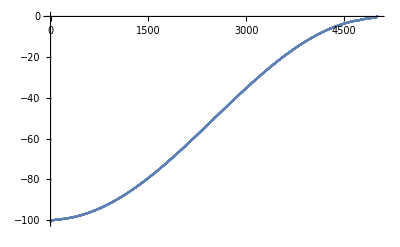

```mathematica
ListPlot[realPartEigenvaluesSorted]
```